-Graphics- |   Métodos Computacionales en Álgebra para Informáticos
Matemática Discreta y Lógica
Dpto. de Matemáticas. Área de  Álgebra  (M. A. García, C. Ordóñez, J. F. Ruiz)

# Capítulo 4 Programación en Mathematica

## 1. Expresiones lógicas

#### Ejemplo 4.1.

Si queremos comprobar si un valor x pertenece al intervalo  [1, 4[, lo haremos escribiendo:

```mathematica
x=3;
1<=x<4
```

True

#### Ejemplo 4.2.

Si queremos comprobar si un valor x pertenece al intervalo  [1, 400[ y es un número primo, lo haremos escribiendo:

```mathematica
x=31;
1<=x<400&&PrimeQ[x]
```

True

O bien:

```mathematica
x=31;
1≤x<400∧PrimeQ[x]
```

True

```mathematica
x=31;
And[1≤x<400,PrimeQ[x]]
```

True

## 2. Órdenes condicionales

### 2.1. El condicional If

#### Ejemplo 4.3.

En este sencillo ejemplo se comprueba si la variable a pertenece al intervalo ]0, 3[ o la variable b es igual a 10, devolviendo “verdadero” en caso afirmativo o “falso” en caso contrario.

```mathematica
a=1;
b=1;
If[(0<a<3)||(b==10),Print["verdadero"],Print["falso"]]
```

verdadero

```mathematica
a=4;
b=1;
If[(0<a<3)||(b==10),Print["verdadero"],Print["falso"]]
```

falso

#### Ejemplo 4.4.

Determinar si x es natural o entero.

```mathematica
x=2;
If[IntegerQ[x], Print["Es entero"]]
If[IntegerQ[x]&&x<0,,Print["Es natural"]]
```

Es entero

Es natural

#### Ejemplo 4.5.

También podemos usar If[] para definir variables o funciones:

```mathematica
valorabsoluto[x_]:=If[x<0,-x,x];
lista={1,2,-1,-2,0};
Table[valorabsoluto[lista[[i]]],{i,Length[lista]}]
```

{1,2,1,2,0}

### 2.2. Otros condicionales: Which, Switch y Piecewise

#### 2.2.1 Which

#### Ejemplo 4.6.

Se puede usar para definir funciones a trozos, por ejemplo:

```mathematica
f[x_]:=Which[0<=x<=1,x^2,1<=x<=2,2-x^2,True,0]
f[0.5]
f[3]
```

0.25

0

#### 2.2.2 Swhich

#### Ejemplo 4.7.

La siguiente función sustituye letras por la posición que tienen en el abecedario:

```mathematica
f[variable_]:=Switch[variable,a,1,b,2,c,3,d,4,e,5,f,6,g,7,h,8,i,9,j,10,k,11,l,12,m,13,n,14,ñ,15,o,16,p,17,q,18,r,19,s,20,t,21,u,22,v,23,w,24,x,25,y,26,z,27];
lista={a,l,g,e,b,r,a};
Table[f[lista[[i]]],{i,Length[lista]}]
```

{1,12,7,5,2,19,1}

#### 2.2.3 Piecewise

#### Ejemplo 4.8.

Definimos la misma función del ejemplo 4.6.:

```mathematica
g[x_]:=Piecewise[{{x^2,0≤x≤1},{2-x^2,1≤x≤2}},0]
g[0.5]
g[3]
```

0.25

0

## 3. Bucles y estructuras de control

#### Ejemplo 4.9.

Observemos como funciona i++,

```mathematica
i=7;
i++
i
```

7

8

Por otra parte, ++i,

```mathematica
i=7;
++i
i
```

8

8

### 3.1. El bucle Do

#### Ejemplo 4.10.

Este bucle comienza con el contador j en el valor inicial 1, incrementa j en dos unidades en cada ciclo, hasta que j alcanza el valor final 7, por tanto el cuerpo lo ejecutará cuatro veces y en cada ciclo calcula e imprime el valor de j2.

```mathematica
Do[Print[j^2],{j,1,7,2}]
```

1

9

25

49

#### Ejemplo 4.11.

Evaluar la función f(x, y) = x2 + y2 en todos los pares de valores enteros (x, y) tales que 4 ≤ x ≤ 8 y 0 ≤ y ≤ 2.

```mathematica
f[x_,y_]:=x^2+y^2
Do[Do[Print["f(",i,",",j,") = ",f[i,j]],{j,0,2}],{i,4,8}]
```

f(4,0) = 16

f(4,1) = 17

f(4,2) = 20

f(5,0) = 25

f(5,1) = 26

f(5,2) = 29

f(6,0) = 36

f(6,1) = 37

f(6,2) = 40

f(7,0) = 49

f(7,1) = 50

f(7,2) = 53

f(8,0) = 64

f(8,1) = 65

f(8,2) = 68

### 3.2. El bucle For

#### Ejemplo 4.12.

Este bucle comienza con j = 1. Parará cuando j sea mayor o igual a 8 e incrementa j una unidad en cada ciclo, luego repetirá la ejecución del cuerpo siete veces y en cada ciclo suma a t, 2 unidades, mostrando en pantalla el valor de t.

```mathematica
t=0;
For[j=1,j<8,j++,t=t+2;Print[t]];
```

2

4

6

8

10

12

14

#### Ejemplo 4.13.

Calcular todos los números primos comprendidos entre 50 y 100.

```mathematica
For[j=50,j<100,j++,If[PrimeQ[j],Print[j]]];
```

53

59

61

67

71

73

79

83

89

97

### 3.3. El bucle While

#### Ejemplo 4.14.

Este bucle comienza con n = 500 y termina cuando n sea mayor o igual a 1000, el contador n se incrementa 50 unidades en cada ciclo, imprimiendo en pantalla el valor de la variable contador en cada ciclo.

```mathematica
n=500;
While[n<1000,n=n+50;Print[n]]
```

550

600

650

700

750

800

850

900

950

1000

#### Ejemplo 4.15.

Calcular el menor número primo mayor que 200.

```mathematica
a=200;
While[!PrimeQ[a],a++];a
```

211

### 3.4. Otros bucles

#### Ejemplo 4.16.

Comprobemos el funcionamiento de los bucles que se muestran en la tabla 4.2.

Si cogemos una lista de números enteros {1, 3, 5, 7, 9}, podemos calcular el resto de dividir por 2 de cada uno así :

```mathematica
lista={1,3,5,7,9};
Mod[lista,2]
```

{1,1,1,1,1}

O bien,

```mathematica
f[x_]:=x^2-1
f[lista]
```

{0,8,24,48,80}

Para aplicar la misma función varias veces usamos Nest[] o NestWhile[] dependiendo de si queremos aplicarla un número concreto de veces o si queremos aplicarla mientras se cumpla cierta condición, por ejemplo, si queremos aplicar 6 veces f al 2:

```mathematica
Nest[f,2,6]
```

247905749270528

También podremos aplicar a cada elemento de "lista" la función f varias veces, por ejemplo 3 veces:

```mathematica
Nest[f,lista,3]
```

{0,3968,330624,5303808,40947200}

Para aplicar f al valor 2 hasta que el resultado sea mayor que 1000000:

```mathematica
NestWhile[f,2,#≤1000000&]
```

15745023

Por último, veamos cómo funciona FixedPoint[],

```mathematica
g[x_]:=N[Sqrt[x]];
FixedPoint[g,2]
```

1.

```mathematica
NestList[g,2,25]
```

{2,1.41421,1.18921,1.09051,1.04427,1.0219,1.01089,1.00543,1.00271,1.00135,1.00068,1.00034,1.00017,1.00008,1.00004,1.00002,1.00001,1.00001,1.,1.,1.,1.,1.,1.,1.,1.}

### 3.5. Estructuras de control. El control de flujo

#### Ejemplo 4.17.

Si llamamos product al producto de los n primeros enteros pares positivos. ¿Cuál será el mayor valor de n verificando que product < 1000? Utilizar la instrucción Break[] y los tres bucles vistos para calcularlo.

```mathematica
product=1;
n=0;
Do[product=product*i;
If[product>=1000,Break[],n++],{i,2,1000,2}];
Print["n es: ",n]
```

n es: 4

```mathematica
product=1;
n=0;
For[i=2,True,i=i+2,product=product*i;If[product>=1000,Break[],n++]];
Print["n es: ",n]
```

n es: 4

```mathematica
product=1;
n=0;
i=0;
While[True,i=i+2;
product=product*i;If[product>=1000,Break[],n++]];
Print["n es: ",n]
```

n es: 4

Sin Break[]

```mathematica
product=1;
n=0;
Do[product=product*i;
If[product≥1000,i=1000,n++],{i,2,1000,2}];
Print["n es: ",n]
```

n es: 4

```mathematica
product=1;
n=-1;
For[i=2,product<1000,i=i+2,product=product*i;n++];
Print["n es: ",n]
```

n es: 4

```mathematica
product=1;
n=-1;
i=0;
While[product<1000,i=i+2;product=product*i;n++];
Print["n es: ",n]
```

n es: 4

#### Ejemplo 4.18.

Calculamos todos los primos comprendidos entre 1 y 100:

```mathematica
Do[If[!PrimeQ[i],Continue[]];
Print[i];,{i,100}];
```

2

3

5

7

11

13

17

19

23

29

31

37

41

43

47

53

59

61

67

71

73

79

83

89

97

#### Ejemplo 4.19.

Calculamos el primer múltiplo mayor que cero de 5 y 11:

```mathematica
variable=Do[If[Mod[i,5]==0&&Mod[i,11]==0,Return[i]],{i,100}];
variable
```

55

## 4. Representaciones gráficas

#### Ejemplo 4.20.

Dibujar la representación analógica de la hora de un reloj.

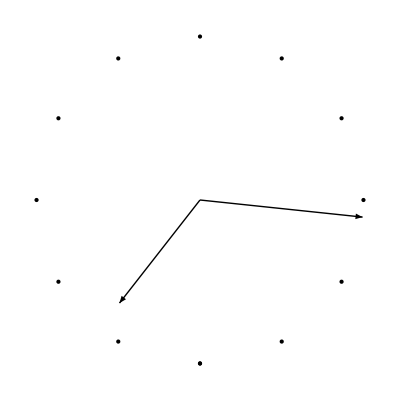

```mathematica
hora=7;
minuto=16;
hora=3-(hora+minuto/60);
minuto=15-minuto;
reloj={};
Do[AppendTo[reloj,Point[{Sin[j],Cos[j]}]],{j,-Pi,Pi,2*Pi/12}];
AppendTo[reloj,Arrow[{{0,0},{Cos[(2*Pi)*(hora/12)]*0.8,Sin[(2*Pi)*(hora/12)]*0.8}}]];
AppendTo[reloj,Arrow[{{0,0},{Cos[(2*Pi)*(minuto/60)],Sin[(2*Pi)*(minuto/60)]}}]];
Show[Graphics[reloj]]
```

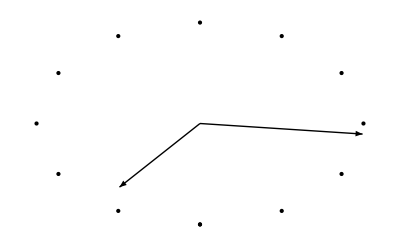

```mathematica
Show[Graphics[reloj,AspectRatio->1/GoldenRatio]]
```

#### Ejemplo 4.21.

Definir una función cuyos argumentos sean la hora expresada en horas, minutos y segundos, y que dibuje la representación analógica.

```mathematica
RJ[hora_,minuto_,segundo_]:=Module[{reloj={},j,hora2,minuto2,segundo2},hora2=3-(hora+minuto/60);
minuto2=15-minuto;
segundo2=15-segundo;AppendTo[reloj,{RGBColor[1,1,.7],Disk[{0,0},1.1]}];AppendTo[reloj,Thickness->0.0175];
AppendTo[reloj,{Blue,Circle[{0,0},1.1]}];AppendTo[reloj,PointSize->.03];
Do[AppendTo[reloj,{Black,Point[{.95*Sin[j],.95*Cos[j]}]}];
AppendTo[reloj,Text[(j/Pi*6)+7,{.85*Sin[j+(7*Pi/6)],.85*Cos[j+(7*Pi/6)]}]];,{j,-Pi,Pi-.1,2*Pi/12}];AppendTo[reloj,Thickness->0.00175];
Do[AppendTo[reloj,Line[{{.9*Sin[j],.9*Cos[j]},{Sin[j],Cos[j]}}]];,{j,-Pi,Pi,2*Pi/60}];AppendTo[reloj,Thickness->0.0175];
AppendTo[reloj,Line[{{0,0},{Cos[(2*Pi)*(hora2/12)]*.8,Sin[(2*Pi)*(hora2/12)]*.8},{-Cos[(2*Pi)*(hora2/12)]*.1,-Sin[(2*Pi)*(hora2/12)]*.1}}]];AppendTo[reloj,Thickness->0.0125];
AppendTo[reloj,Line[{{Cos[(2*Pi)*(minuto2/60)]*.9,Sin[(2*Pi)*(minuto2/60)]*.9},{-Cos[(2*Pi)*(minuto2/60)]*.1,-Sin[(2*Pi)*(minuto2/60)]*.1}}]];AppendTo[reloj,Thickness->0.01];
AppendTo[reloj,Line[{{Cos[(2*Pi)*(segundo2/60)],Sin[(2*Pi)*(segundo2/60)]},{-Cos[(2*Pi)*(segundo2/60)]/5,-Sin[(2*Pi)*(segundo2/60)]/5}},VertexColors->{Red,Blue}]];Show[Graphics[reloj],Background->RGBColor[0.84,0.92,1.]]]
```

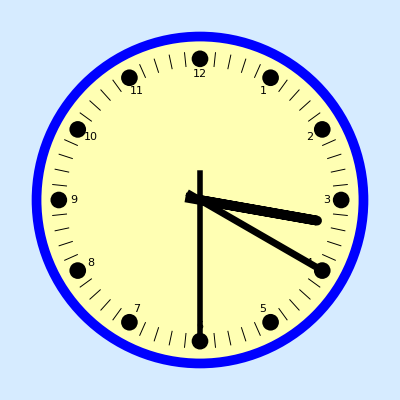

```mathematica
RJ[15,20,30]
```

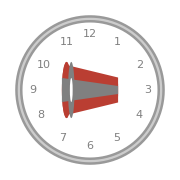

```mathematica
ClockGauge[{15,20,30}]
```

#### Ejemplo 4.22.

En este ejemplo vamos a representar gráficamente el problema y la solución al problema de las Torres de Hanoi del ejemplo 2.24.

```mathematica
Movimientos={};
Hanoi[n_,MontonOrigen_,MontonAuxiliar_,MontonDestino_]:=Module[{},If[n==1,AppendTo[Movimientos,{MontonOrigen,MontonDestino}];,Hanoi[n-1,MontonOrigen,MontonDestino,MontonAuxiliar];
AppendTo[Movimientos,{MontonOrigen,MontonDestino}];
Hanoi[n-1,MontonAuxiliar,MontonOrigen,MontonDestino];];];
```

```mathematica
Movimientos={};
Hanoi[10,1,2,3];
```

```mathematica
n=10;
```

```mathematica
Montones={Table[i,{i,n,1,-1}],{},{}};
MovimientosFichas={Montones};
Do[
AppendTo[Montones[[Movimientos[[i]][[2]]]],Montones[[Movimientos[[i]][[1]]]][[Length[Montones[[Movimientos[[i]][[1]]]]]]]];
Montones[[Movimientos[[i]][[1]]]]=Delete[Montones[[Movimientos[[i]][[1]]]],Length[Montones[[Movimientos[[i]][[1]]]]]];
AppendTo[MovimientosFichas,Montones];
,{i,1,Length[Movimientos]}];
```

```mathematica
Representar3D[movimiento_,k_]:=Module[{i,j,Objetos},Objetos={Black,Text[Style["Torres de Hanói",Large,Bold,Red],{-n-1,(n+1)*2,n+4}],Text[k,{-n-1,(n+1)*5,n+5}],Orange,Cuboid[{-1-n,-n-1,-1/2},{n+1,(n+1)*5,0}],Cuboid[{-2-n,-n-2,-1},{n+2,(n+1)*5+1,-1/2}],Cylinder[{{0,0,0},{0,0,n+4}},1/2],Cylinder[{{0,(n+1)*2,0},{0,(n+1)*2,n+4}},1/2],Cylinder[{{0,(n+1)*4,0},{0,(n+1)*4,n+4}},1/2],White};Do[Do[AppendTo[Objetos,Cylinder[{{0,(n+1)*2*(i-1),(j-1)},{0,(n+1)*2*(i-1),j}},movimiento[[i]][[j]]]];,{j,Length[movimiento[[i]]]}];,{i,3}];Graphics3D[Objetos,BoxStyle->Directive[Dashed,Gray],ViewPoint->{Pi,0,Pi/3},ImageSize->600]];
```

```mathematica
Grafico={};
Do[AppendTo[Grafico,Representar3D[MovimientosFichas[[k]],k]];,{k,Length[MovimientosFichas]}];
```

```mathematica
ListAnimate[Grafico,.75]
```

## 5. Ejercicios

#### Ejercicio 4.8.

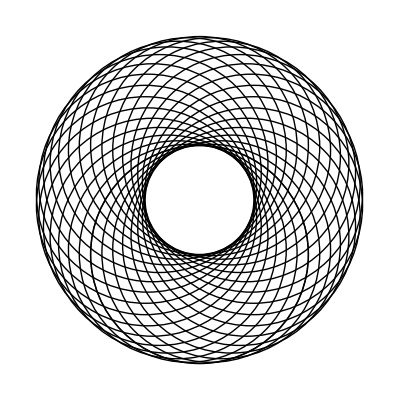

```mathematica
n=30;
radio=2;
circulos={};
Do[AppendTo[circulos,Circle[{Sin[j],Cos[j]},radio]],{j,-Pi,Pi,2*Pi/n}];
Show[Graphics[circulos],AspectRatio->Automatic]
```

#### Ejercicio 4.11.

Las funciones cuyas entradas son las tres coordenadas de un punto tridimensional y cuyas salidas, respectivas, son la coordenada x e y de su representación en el plano son:

```mathematica
CoorX[x_,y_,z_]:=x-((z/2.5)*Sin[Pi/3])
CoorY[x_,y_,z_]:=y-((z/2.5)*Cos[Pi/3])
```

Sabiendo que la ecuación de una esfera de centro (0, 0, 0) y radio r es x^2 + y^2 + z^2 = r^2. Usamos las funciones anteriores para representar un número suficiente de puntos de la esfera de radio 3 que nos permita distinguir su forma.

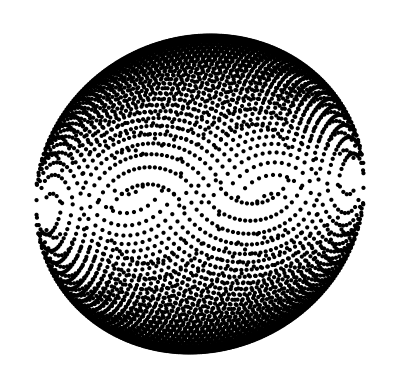

Número de puntos usados: 5618

```mathematica
puntos={};
x=0;y=0;z=0;
Do[Do[If[9-(z^2+x^2)>0,y=Sqrt[9-(z^2+x^2)];
AppendTo[puntos,Point[{CoorX[x,y,z],CoorY[x,y,z]}]];
AppendTo[puntos,Point[{CoorX[x,-y,z],CoorY[x,-y,z]}]]];,{x,-3,3,.1}];,{z,-3,3,.1}];
Show[Graphics[puntos],AspectRatio->Automatic]
Print["Número de puntos usados: ",Length[puntos]];
```

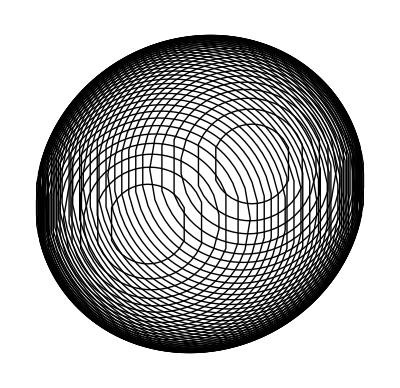

```mathematica
puntos={};
graficos={};
Do[puntos={};
Do[If[9-(z^2+x^2)≥0,y=Sqrt[9-(z^2+x^2)];
AppendTo[puntos,{CoorX[x,y,z],CoorY[x,y,z]}]];,{x,-3,3,.1}];
Do[If[9-(z^2+x^2)≥0,y=-Sqrt[9-(z^2+x^2)];
AppendTo[puntos,{CoorX[x,y,z],CoorY[x,y,z]}]];,{x,3,-3,-.1}];
If[Length[puntos]>0,AppendTo[puntos,puntos[[1]]]];
AppendTo[graficos,Line[puntos]],{z,-3,3,.1}];
Show[Graphics[graficos],AspectRatio->Automatic]
```

De la misma forma podemos representar cualquier superficie, por ejemplo: z^2 – x^2 =y.

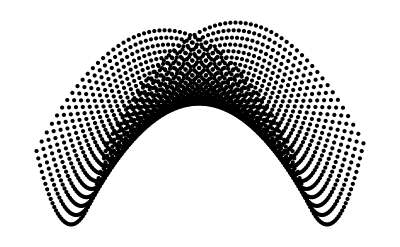

Número de puntos usados: 2091

```mathematica
puntos={};
x=0;y=0;z=0;
Do[Do[y=(z^2-x^2);
AppendTo[puntos,Point[{CoorX[x,y,z],CoorY[x,y,z]}]];,{x,-5,5,.2}];,{z,-4,4,.2}];
Show[Graphics[puntos],AspectRatio->1/GoldenRatio]
Print["Número de puntos usados: ",Length[puntos]];
```

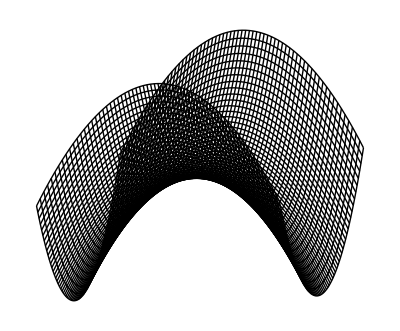

```mathematica
puntos={};
graficos={};
Do[puntos={};
Do[y=(z^2-x^2);
AppendTo[puntos,{CoorX[x,y,z],CoorY[x,y,z]}];,{x,-1,1,.03}];
AppendTo[graficos,Line[puntos]];,{z,-1,1,.03}];
Do[puntos={};
Do[y=(z^2-x^2);
AppendTo[puntos,{CoorX[x,y,z],CoorY[x,y,z]}];,{z,-1,1,.03}];
AppendTo[graficos,Line[puntos]];,{x,-1,1,.03}];
Show[Graphics[graficos],AspectRatio->Automatic]
```